```mathematica
format=".eps";
plotdir="plots";
```

## Setup

```mathematica
(*Needs["PlotLegends`"]*)
SetDirectory[NotebookDirectory[]];
```

```mathematica
Py2List[f0_]:=Module[{f=f0,e},ToExpression["{"<>StringReplace[Import[f],{"e-"->"E-",":"->",","["->"{","]"->"}","'"->"\"","\n"->","}]<>"}"]
]
```

```mathematica
SortBreak[l0_]:=Module[{l=l0,i,b},
b=Reap[For[i=1,i<Length[l],i++,
If[l[[i]][[1]]==0,
Sow[i]
]
]][[2]][[1]];
b=Partition[Riffle[b,Join[b[[2;;]]-1,{Length[l]}]],2];
Map[l[[#[[1]];;#[[2]]]]&,b]
]
```

```mathematica
TrimLegend[p0_]:=Module[{p=p0,r,rp,n,si,i,w,h},
n=p[[1]][[2]][[1]][[1]][[6]][[1]][[1]][[1]]//Length;
si=Select[p[[1]][[2]][[1]][[1]][[6]][[1]][[1]][[1]],StringLength[#[[2]][[1]]]≠0&];
p[[1]][[2]][[1]][[1]][[6]][[1]][[1]][[1]]=si;

rp=Map[Position[p[[1]][[2]][[1]][[1]],#]&,Select[p[[1]][[2]][[1]][[1]],Head[#]==Rectangle&]]//Flatten;
For[i=1,i≤Length[rp],i++,
r=p[[1]][[2]][[1]][[1]][[rp[[i]]]];
{w,h}=r[[2]]-r[[1]];
p[[1]][[2]][[1]][[1]][[rp[[i]]]]=Rectangle[r[[1]]+{0,h (n-Length[si])/n},r[[1]]+{w,h}];
];
p
]
```

## Processing Performance

### Initialization

```mathematica
AbsoluteTiming[
tpn={SortBreak[Import["tun.naive.python.perf"]],SortBreak[Import["tun.naive.pypy.perf"]]};
tpb={SortBreak[Import["tun.born.python.perf"]],SortBreak[Import["tun.born.pypy.perf"]]};
tpp={SortBreak[Import["tun.paxson.python.perf"]],SortBreak[Import["tun.paxson.pypy.perf"]]};
tph={SortBreak[Import["tun.himbeault.python.perf"]],SortBreak[Import["tun.himbeault.pypy.perf"]]};
tpall={tpn,tpb,tpp,tph};
]
```

{0.74109,Null}

```mathematica
AbsoluteTiming[
qrpn={Map[{10#[[1]],#[[2]]}&,Import["qr.naive.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qr.naive.pypy.perf"]]};
qrpb={Map[{10#[[1]],#[[2]]}&,Import["qr.born.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qr.born.pypy.perf"]]};
qrpp={Map[{10#[[1]],#[[2]]}&,Import["qr.paxson.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qr.paxson.pypy.perf"]]};
qrph={Map[{10#[[1]],#[[2]]}&,Import["qr.himbeault.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qr.himbeault.pypy.perf"]]};
qrpall={qrpn,qrpb,qrpp,qrph};
]
```

{0.62508,Null}

```mathematica
AbsoluteTiming[
qrpn={Map[{10#[[1]],#[[2]]}&,Import["qs.naive.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qs.naive.pypy.perf"]]};
qrpb={Map[{10#[[1]],#[[2]]}&,Import["qs.born.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qs.born.pypy.perf"]]};
qrpp={Map[{10#[[1]],#[[2]]}&,Import["qs.paxson.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qs.paxson.pypy.perf"]]};
qrph={Map[{10#[[1]],#[[2]]}&,Import["qs.himbeault.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qs.himbeault.pypy.perf"]]};
qrpall={qrpn,qrpb,qrpp,qrph};
]
```

{2.42365,Null}

```mathematica
AbsoluteTiming[
qrpn={Map[{10#[[1]],#[[2]]}&,Import["qb.naive.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qb.naive.pypy.perf"]]};
qrpb={Map[{10#[[1]],#[[2]]}&,Import["qb.born.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qb.born.pypy.perf"]]};
qrpp={Map[{10#[[1]],#[[2]]}&,Import["qb.paxson.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qb.paxson.pypy.perf"]]};
qrph={Map[{10#[[1]],#[[2]]}&,Import["qb.himbeault.python.perf"]],Map[{10#[[1]],#[[2]]}&,Import["qb.himbeault.pypy.perf"]]};
qrpall={qrpn,qrpb,qrpp,qrph};
]
```

{21.47673,Null}

```mathematica
(* The inputs are permuted in strange ways, fix it *)
(* App order: dns2tcp, dnscat, iodine, prob-dns *)
(* c2s, s2c *)
pv={10,100,1000,10000,100000,1000000,25,250,2500,25000,250000,50,500,5000,50000,500000};
p=Ordering[pv];
```

```mathematica
OrderedMeans[l0_]:=Module[{l=l0,m},
m=Map[Mean[Transpose[#][[2]]]&,l];
Map[Sort[Transpose[{pv,#}]]&,Partition[m,16]]
]
```

```mathematica
colors={Hue[0],Hue[1/4],Hue[2/4],Hue[3/4]};
```

```mathematica
methodlabels={"Naive","Born","Paxson","Himbeault"};
```

### Plotting

```mathematica
ppi=MapIndexed[ListLogLinearPlot[Join[OrderedMeans[#1[[1]]],OrderedMeans[#1[[2]]]],PlotRange->All,Joined->True,PlotStyle->Join[Riffle[Map[{Thick,Darker[#]}&,colors],Map[{Thick,Lighter[#]}&,colors]][[;;7]],Map[{Thick,Dashed,#}&,Riffle[Map[Darker,colors],Map[Lighter,colors]]][[;;7]]],ImageSize->800,PlotLabel->"Performance of Python Interpreters on Tunnel Data - "<>methodlabels[[First[#2]]]<>" Method\nProcessing Speed by Input File (Cython, PyPy)",AxesLabel->{"Tunnel Throughput\n(bytes / second)","Processing Rate\n(packets / second)"},PlotLegends->LineLegend[Join[Map[#<>"\nCython"&,tunlabels],Map[#<>"\nPyPy"&,tunlabels]]]]&,tpall];
MapIndexed[Export[plotdir<>"/"<>"ppi-"<>ToLowerCase[methodlabels[[First[#2]]]]<>format, #1]&,ppi];
```

```mathematica
pmat=ListLogLinearPlot[Join[Map[Mean[OrderedMeans[#[[1]]]]&,tpall],Map[Mean[OrderedMeans[#[[2]]]]&,tpall]],Joined->True,PlotLegends->LineLegend[Join[Map[#<>"\nCython"&,methodlabels],Map[#<>"\nPyPy"&,methodlabels]]],PlotStyle->Join[Table[Thick,{4}],Table[{Thick,Dashed},{4}]],PlotRange->All,ImageSize->800,
PlotLabel->"Performance of Analysis Method on Tunnel Data\nProcessing Speed by Python Interpreter (Cython, PyPy)",AxesLabel->{"Tunnel Throughput\n(bytes / second)","Processing Rate\n(packets / second)"}];
Export[plotdir<>"/"<>"pmat"<>format,pmat];
```

```mathematica
pmqr=ListPlot[Join[Map[#[[1]]&,qrpall],Map[#[[2]]&,qrpall]],Joined->True,PlotLegends->LineLegend[Join[Map[#<>"\nCython"&,methodlabels],Map[#<>"\nPyPy"&,methodlabels]]],PlotStyle->Join[Table[Thick,{4}],Table[{Thick,Dashed},{4}]],PlotRange->{All,All},ImageSize->800,PlotLabel->"Performance of Analysis Method on Real World Data\nProcessing Speed by Python Interpreter (Cython, PyPy)",AxesLabel->{"Position in Input\n(seconds)","Processing Rate\n(packets / second)"}];
Export[plotdir<>"/"<>"pmqr"<>format,pmqr];
pmqr[[1]][[2]][[Position[pmqr[[1]][[2]],Select[pmqr[[1]][[2]],#[[1]]==PlotRange&][[1]]][[1]][[1]]]][[2]]={{0,250},All};
Export[plotdir<>"/"<>"pmqr-250"<>format,pmqr];
```

## Detection Performance

### Initialization

```mathematica
MakeCumulative[l0_]:=Module[{l=l0,t,i,s=0},
t=Tally[l];
Join[{{0,1}},Reap[For[i=1,i<Length[t],i++,
s+=t[[i]][[2]];
Sow[{t[[i]][[1]],1-s/Length[l]}];
]][[2]][[1]]]
]
```

```mathematica
methodlabels={"Naive","Born","Paxson","Himbeault"};
tunapplabels={"DNS2TCP","DNSCat","Iodine","Prob-code"};
```

```mathematica
AbsoluteTiming[
tunall={Py2List["tun.naive.python"],Py2List["tun.born.python"],Py2List["tun.paxson.python"],Py2List["tun.himbeault.python"]};
(*tl=Map[Sort[Flatten[Map[#[[2]]&,Flatten[Map[#[[4;;]]&,#],1]]]]&,tunall];*)
tl=Map[Sort[Flatten[Map[#[[4;;]][[1]][[2]]&,#]]]&,tunall];
tlc=Map[MakeCumulative,tl];
tlci=Map[Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[#]]&,tlc];
{tnlci,tblci,tplci,thlci}=tlci;
]
```

{0.43906,Null}

```mathematica
AbsoluteTiming[
(* Separated by method, then by tunnel application *)
tunsep=Map[{Join[#[[1]],#[[2]]],Join[#[[3]],#[[4]]],Join[#[[5]],#[[6]]],#[[7]]}&,Map[Partition[#,16]&,tunall]];
(*ttl=Map[Map[Sort[Flatten[Map[Map[#[[2]]&,#[[4;;]]]&,#]]]&,#]&,tunsep];*)
ttl=Map[Map[Sort[Flatten[Map[#[[4;;]][[1]][[2]]&,#]]]&,#]&,tunsep];
ttlc=Map[Map[MakeCumulative,#]&,ttl];
ttlci=Map[Map[Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[#]]&,#]&,ttlc];
]
```

{0.097012,Null}

```mathematica
AbsoluteTiming[
mintun=Map[Map[Map[
Sort[
Map[{
Total[Map[Total[#[[2]]]/Length[#[[2]]]&,Flatten[tunsep[[1]],1][[Position[Flatten[tunsep[[1]],1],#[[1]]][[1]][[1]]]][[4;;]]]],
Min[#[[4]][[2]]]}&,#]
]&,Partition[#,16]]&,#]&,tunsep];
avgtun=Map[Map[Map[
Sort[
Map[{
Total[Map[Total[#[[2]]]/Length[#[[2]]]&,Flatten[tunsep[[1]],1][[Position[Flatten[tunsep[[1]],1],#[[1]]][[1]][[1]]]][[4;;]]]],
Mean[#[[4]][[2]]]}&,#]
]&,Partition[#,16]]&,#]&,tunsep];
medtun=Map[Map[Map[
Sort[
Map[{
Total[Map[Total[#[[2]]]/Length[#[[2]]]&,Flatten[tunsep[[1]],1][[Position[Flatten[tunsep[[1]],1],#[[1]]][[1]][[1]]]][[4;;]]]],
Median[#[[4]][[2]]]}&,#]
]&,Partition[#,16]]&,#]&,tunsep];
maxtun=Map[Map[Map[
Sort[
Map[{
Total[Map[Total[#[[2]]]/Length[#[[2]]]&,Flatten[tunsep[[1]],1][[Position[Flatten[tunsep[[1]],1],#[[1]]][[1]][[1]]]][[4;;]]]],
Max[#[[4]][[2]]]}&,#]
]&,Partition[#,16]]&,#]&,tunsep];
]
```

{0.44505,Null}

```mathematica
AbsoluteTiming[
qrall={Py2List["qr.naive.python"][[1]],Py2List["qr.born.python"][[1]],Py2List["qr.paxson.python"][[1]],Py2List["qr.himbeault.python"][[1]]};
qrl=Map[Sort[Flatten[Join[Map[#[[2]]&,#[[4;;]]]]]]&,qrall];
qrlc=Map[MakeCumulative,qrl];
qrlci=Map[Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[#]]&,qrlc];
{qrnlci,qrblci,qrplci,qrhlci}=qrlci;
]
```

{14.50684,Null}

```mathematica
AbsoluteTiming[
qrall={Py2List["qs.naive.python"][[1]],Py2List["qs.born.python"][[1]],Py2List["qs.paxson.python"][[1]],Py2List["qs.himbeault.python"][[1]]};
qrl=Map[Sort[Flatten[Join[Map[#[[2]]&,#[[4;;]]]]]]&,qrall];
qrlc=Map[MakeCumulative,qrl];
qrlci=Map[Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[#]]&,qrlc];
{qrnlci,qrblci,qrplci,qrhlci}=qrlci;
]
```

{109.40718,Null}

```mathematica
AbsoluteTiming[
Get["qb.born.mx"];
Get["qb.naive.mx"];
Get["qb.himbeault.mx"];
Get["qb.paxson.mx"];
qrlci={qrnlci,qrblci,qrplci,qrhlci};
]
```

{8.09503,Null}

```mathematica
AbsoluteTiming[
(*qrall={Py2List["qb.naive.python"][[1]],Py2List["qb.born.python"][[1]],Py2List["qb.paxson.python"][[1]],Py2List["qb.himbeault.python"][[1]]};*)
(*qrall={Py2List["qb.naive.python"][[1]],{},{},{}};*)
(*qrall={{},{},Py2List["qb.paxson.python"][[1]],{}};*)
qrall={{},{},{},Py2List["qb.himbeault.python"][[1]]};
qrl=Map[Sort[Flatten[Join[Map[#[[2]]&,#[[4;;]]]]]]&,qrall];
(*qrl={{},Sort[Transpose[Import["qb.born.csv"]]],{},{}};*)
qrlc=Map[MakeCumulative,qrl];
qrlci=Map[Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[#]]&,qrlc];
{qrnlci,qrblci,qrplci,qrhlci}=qrlci;
]
```

{243.46994,Null}

```mathematica
(* style=Map[Join[{Thick},#]&,{{Darker[Hue[0]]},{Darker[Hue[0.6]]},{Dashed,Darker[Hue[1/8]]},{Dashed,Darker[Hue[3/8]]},{Dashed,Darker[Hue[5/8]]},{Dashed,Darker[Hue[7/8]]}}]; *)
style=Map[Join[{Thick},{#}]&,{Lighter[Hue[0]],Lighter[Hue[0.6]],Darker[Hue[1/8]],Darker[Hue[3/8]],Darker[Hue[5/8]],Darker[Hue[7/8]]}]; 
vlstyle=Flatten[Map[{Directive[Thick,#],Directive[Thick,Dashed,#]}&,Table[Darker[Hue[i/Ceiling[Length[inrate]/2]]],{i,0,Ceiling[Length[inrate]/2]-1}]]];
nlines=3;
```

### Plotting

```mathematica
mpbttstyle=Riffle[
Map[{Thick,Darker[#]}&,{Hue[0],Hue[1/4],Hue[2/4],Hue[3/4]}],
Map[Join[{Thick,Dashed,#}]&,Map[Darker,{Hue[0],Hue[1/4],Hue[2/4],Hue[3/4]}]]
];
mpbtt=Legended[GraphicsGrid[{{Show[ListLogLogPlot[Flatten[medtun[[1]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],ListLogLogPlot[Flatten[avgtun[[1]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],PlotLabel->"Detection Performance by Tunnel Application and Throughput\nNaive Metric",AxesLabel->{"Observed\nThroughput\n(bytes / second)","Metric"},ImageSize->400],
Show[ListLogLogPlot[Flatten[medtun[[2]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],ListLogLogPlot[Flatten[avgtun[[2]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],PlotLabel->"Detection Performance by Tunnel Application and Throughput\nBorn Metric",AxesLabel->{"Observed\nThroughput\n(bytes / second)","Metric"},ImageSize->400]
},{
Show[ListLogLogPlot[Flatten[medtun[[3]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],ListLogLogPlot[Flatten[avgtun[[3]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],PlotLabel->"Detection Performance by Tunnel Application and Throughput\nPaxsom Metric",AxesLabel->{"Observed\nThroughput\n(bytes / second)","Metric"},ImageSize->400],
Show[ListLogLogPlot[Flatten[medtun[[4]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],ListLogLogPlot[Flatten[avgtun[[4]],1],Joined->True,PlotRange->All,PlotStyle->mpbttstyle],PlotLabel->"Detection Performance by Tunnel Application and Throughput\nHimbeault Metric",AxesLabel->{"Observed\nThroughput\n(bytes / second)","Metric"},ImageSize->400]}}],
LineLegend[Map[Directive[Flatten[{#,Line[{{0,0},{1,0}}]}]]&,mpbttstyle][[;;-2]],Riffle[Map[#<>" client-to-server"&,tunapplabels],Map[#<>" server-to-client"&,tunapplabels]][[;;-2]]]];
Export[plotdir<>"/"<>"mpbtt"<>format,mpbtt];
```

```mathematica
mpn=
Legended[
ParametricPlot[{{qrlci[[1]][[1]][t],qrlci[[1]][[2]][t]},{tlci[[1]][[1]][t],tlci[[1]][[2]][t]},{ttlci[[1]][[1]][[1]][t],ttlci[[1]][[1]][[2]][t]},{ttlci[[1]][[2]][[1]][t],ttlci[[1]][[2]][[2]][t]},{ttlci[[1]][[3]][[1]][t],ttlci[[1]][[3]][[2]][t]},{ttlci[[1]][[4]][[1]][t],ttlci[[1]][[4]][[2]][t]}},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,2000},{0,1}},ImageSize->800,
PlotStyle->style,
PlotLabel->"Detection Performance\nNaive Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"}],
LineLegend[Map[Directive[#[[1]],#[[2]]]&,style],Join[{"Normal", "Tunnel Aggregate"},tunapplabels]]];
(*
Export[plotdir<>"/"<>"mpn"<>format,mpn];
*)
```

```mathematica
mpnv=
Legended[
ParametricPlot[{qrlci[[1]][[1]][t],qrlci[[1]][[2]][t]},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,2000},{0,1}},ImageSize->800,
PlotStyle->{Thick,Black},
PlotLabel->"Detection Performance\nNaive Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"},
Epilog->Flatten[Map[
MapIndexed[Flatten[{vlstyle[[#2[[1]]]],#}]&,#]
&,
Transpose[
Map[
Map[
Line[{{#[[2]],-1},{#[[2]],1}}]
&,#[[;;nlines]]]
&,Flatten[avgtun[[1]],1]]
]],1]
],
LineLegend[Join[{Directive[Thick,Black]},vlstyle],Join[{"Normal"},tunlabels]]];
cn=Map[(0.25-#(1-#))/0.25&,
qrlci[[1]][[2]][t]/.Map[FindRoot[qrlci[[1]][[1]][t]==#,{t,0.5,0,1}]&,Flatten[avgtun[[1]],1][[All,1,2]]]
]
Export[plotdir<>"/"<>"mpnv"<>format,mpnv];
```

{0.992602,0.978229,0.856938,0.811349,0.99343,0.99343,0.705662}

```mathematica
mpb=Legended[ParametricPlot[{{qrlci[[2]][[1]][t],qrlci[[2]][[2]][t]},{tlci[[2]][[1]][t],tlci[[2]][[2]][t]},{ttlci[[2]][[1]][[1]][t],ttlci[[2]][[1]][[2]][t]},{ttlci[[2]][[2]][[1]][t],ttlci[[2]][[2]][[2]][t]},{ttlci[[2]][[3]][[1]][t],ttlci[[2]][[3]][[2]][t]},{ttlci[[2]][[4]][[1]][t],ttlci[[2]][[4]][[2]][t]}},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,1.0},{0,1}},ImageSize->800,
PlotStyle->style,
PlotLabel->"Detection Performance\nBorn Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"}],
LineLegend[Map[Directive[#[[1]],#[[2]]]&,style],Join[{"Normal", "Tunnel Aggregate"},tunapplabels]]];
(*
Export[plotdir<>"/"<>"mpb"<>format,mpb];
*)
```

```mathematica
mpbv=
Legended[
ParametricPlot[{qrlci[[2]][[1]][t],qrlci[[2]][[2]][t]},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,1.0},{0,1}},ImageSize->800,
PlotStyle->{Thick,Black},
PlotLabel->"Detection Performance\nBorn Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"},
Epilog->Flatten[Map[
MapIndexed[Flatten[{vlstyle[[#2[[1]]]],#}]&,#]
&,
Transpose[
Map[
Map[
Line[{{#[[2]],-1},{#[[2]],1}}]
&,#[[;;nlines]]]
&,Flatten[avgtun[[2]],1]]
]],1]],
LineLegend[Join[{Directive[Thick,Black]},vlstyle],Join[{"Normal"},tunlabels]]];
cb=Map[(0.25-#(1-#))/0.25&,
qrlci[[2]][[2]][t]/.Map[FindRoot[qrlci[[2]][[1]][t]==#,{t,0.5,0,1}]&,Flatten[avgtun[[2]],1][[All,1,2]]]
]
Export[plotdir<>"/"<>"mpbv"<>format,mpbv];
```

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {5.55112×10^-17}. Try perturbing the initial point(s).

FindRoot::jsing: Encountered a singular Jacobian at the point {t} = {0.}. Try perturbing the initial point(s).

{0.789285,0.687144,0.794868,0.0707182,1.,1.,0.00344502}

```mathematica
mpp=Legended[ParametricPlot[{{qrlci[[3]][[1]][t],qrlci[[3]][[2]][t]},{tlci[[3]][[1]][t],tlci[[3]][[2]][t]},{ttlci[[3]][[1]][[1]][t],ttlci[[3]][[1]][[2]][t]},{ttlci[[3]][[2]][[1]][t],ttlci[[3]][[2]][[2]][t]},{ttlci[[3]][[3]][[1]][t],ttlci[[3]][[3]][[2]][t]},{ttlci[[3]][[4]][[1]][t],ttlci[[3]][[4]][[2]][t]}},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,2000},{0,1}},ImageSize->800,
PlotStyle->style,
PlotLabel->"Detection Performance\nPaxson Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"}],
LineLegend[Map[Directive[#[[1]],#[[2]]]&,style],Join[{"Normal", "Tunnel Aggregate"},tunapplabels]]];
(*
Export[plotdir<>"/"<>"mpp"<>format,mpp];
*)
```

```mathematica
mppv=
Legended[
ParametricPlot[{qrlci[[3]][[1]][t],qrlci[[3]][[2]][t]},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,2000},{0,1}},ImageSize->800,
PlotStyle->{Thick,Black},
PlotLabel->"Detection Performance\nPaxson Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"},
Epilog->Flatten[Map[
MapIndexed[Flatten[{vlstyle[[#2[[1]]]],#}]&,#]
&,
Transpose[
Map[
Map[
Line[{{#[[2]],-1},{#[[2]],1}}]
&,#[[;;nlines]]]
&,Flatten[avgtun[[3]],1]]
]],1]],
LineLegend[Join[{Directive[Thick,Black]},vlstyle],Join[{"Normal"},tunlabels]]];
cp=Map[(0.25-#(1-#))/0.25&,
qrlci[[3]][[2]][t]/.Map[FindRoot[qrlci[[3]][[1]][t]==#,{t,0.5,0,1}]&,Flatten[avgtun[[3]],1][[All,1,2]]]
]
Export[plotdir<>"/"<>"mppv"<>format,mppv];
mppv[[1]][[2]][[Position[mppv[[1]][[2]],Select[mppv[[1]][[2]],#[[1]]==PlotRange&][[1]]][[1]][[1]]]][[2]]={{0,500},{0,1}};
Export[plotdir<>"/"<>"mppv-500"<>format,mppv];
```

{0.993095,0.959925,0.906398,0.909335,0.99843,0.997689,0.916664}

```mathematica
mph=Legended[ParametricPlot[{{qrlci[[4]][[1]][t],qrlci[[4]][[2]][t]},{tlci[[4]][[1]][t],tlci[[4]][[2]][t]},{ttlci[[4]][[1]][[1]][t],ttlci[[4]][[1]][[2]][t]},{ttlci[[4]][[2]][[1]][t],ttlci[[4]][[2]][[2]][t]},{ttlci[[4]][[3]][[1]][t],ttlci[[4]][[3]][[2]][t]},{ttlci[[4]][[4]][[1]][t],ttlci[[4]][[4]][[2]][t]}},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,2000},{0,1}},ImageSize->800,
PlotStyle->style,
PlotLabel->"Detection Performance\nHimbeault Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"}],
LineLegend[Map[Directive[#[[1]],#[[2]]]&,style],Join[{"Normal", "Tunnel Aggregate"},tunapplabels]]];
(*
Export[plotdir<>"/"<>"mph"<>format,mph];
mph[[1]][[2]][[Position[mph[[1]][[2]],Select[mph[[1]][[2]],#[[1]]==PlotRange&][[1]]][[1]][[1]]]][[2]]={{0,100},{0,1}};
Export[plotdir<>"/"<>"mph-100"<>format,mph];
*)
```

```mathematica
mphv=
Legended[
ParametricPlot[{qrlci[[4]][[1]][t],qrlci[[4]][[2]][t]},
{t,0,1},AspectRatio->1/GoldenRatio,PlotRange->{{0,2000},{0,1}},ImageSize->800,
PlotStyle->{Thick,Black},
PlotLabel->"Detection Performance\nHimbeault Metric",AxesLabel->{"Metric","Probability of Metric\ngreater than X"},
Epilog->Flatten[Map[
MapIndexed[Flatten[{vlstyle[[#2[[1]]]],#}]&,#]
&,
Transpose[
Map[
Map[
Line[{{#[[2]],-1},{#[[2]],1}}]
&,#[[;;nlines]]]
&,Flatten[avgtun[[4]],1]]
]],1]],
LineLegend[Join[{Directive[Thick,Black]},vlstyle],Join[{"Normal"},tunlabels]]];
ch=Map[(0.25-#(1-#))/0.25&,
qrlci[[4]][[2]][t]/.Map[FindRoot[qrlci[[4]][[1]][t]==#,{t,0.5,0,1}]&,Flatten[avgtun[[4]],1][[All,1,2]]]
]
Export[plotdir<>"/"<>"mphv"<>format,mphv];
mphv[[1]][[2]][[Position[mphv[[1]][[2]],Select[mphv[[1]][[2]],#[[1]]==PlotRange&][[1]]][[1]][[1]]]][[2]]={{0,100},{0,1}};
Export[plotdir<>"/"<>"mphv-100"<>format,mphv];
```

{0.996097,0.99419,0.989046,0.97018,0.999979,0.999977,0.927397}

```mathematica
cplot=BarChart[{cn,cb,cp,ch},Joined->True,PlotRange->{0,1},PlotLabel->"Certainty of Tunnel Detection",ChartStyle->{Darker[Red],Darker[Darker[Red]],Darker[Blue],Darker[Darker[Blue]],Darker[Green],Darker[Darker[Green]],Black},ChartLegends->tunlabels,
ChartLabels->{{"Naive","Born","Paxson","Himbeault"},None},ImagePadding->10,ImageSize->500];
Export[plotdir<>"/"<>"cplot"<>format,cplot];
```

## Tunnel Application Performance

### Initialization

```mathematica
ratenames={"rate.dns2tcp.c.csv","rate.dns2tcp.s.csv","rate.dnscat2.c.csv","rate.dnscat2.s.csv",
"rate.iodine.c.csv","rate.iodine.s.csv","rate.prob-dns3.c.csv"};
tunlabels={"dns2tcp c2s","dns2tcp s2c","dnscat c2s","dnscat s2c","iodine c2s","iodine s2c","prob-dns c2s"};
ratedata=Map[Partition[Import[#][[2;;]],2]&,ratenames];
inrate=MapIndexed[
{ratenames[[#2]],Map[{#[[1]][[1]],Mean[Map[ToExpression,#[[2]]][[2;;-2]]]//N}&,#]}&,
ratedata];
outrate=Map[
Sort[Transpose[{pv,Map[
Mean[#[[4]][[2]]]/10&,
#]}]]&,
Partition[Flatten[tunsep[[1]],1],16]
];
```

### Plotting

```mathematica
tunrates=Legended[GraphicsGrid[
Partition[Append[
MapIndexed[
Show[
ListLogLogPlot[{#[[1]][[2]],#[[2]][[2]]},PlotStyle->Flatten[Map[{Directive[Thick,#],Directive[Thick,Dashed,#]}&,Table[Darker[Hue[i/Ceiling[Length[inrate]/2]]],{i,0,Ceiling[Length[inrate]/2]-1}]]][[2(#2[[1]]-1)+1;;2#2[[1]]]],Joined->True,PlotRange->All,ImageSize->400,AxesLabel->{"",If[#2[[1]]==1,"Output\n(bytes / second)"]}],
ListLogLogPlot[outrate[[2(#2[[1]]-1)+1;;2#2[[1]]]],PlotStyle->Flatten[Map[{Directive[Thick,#],Directive[Thick,Dashed,#]}&,Table[Lighter[Hue[i/Ceiling[Length[inrate]/2]]],{i,0,Ceiling[Length[inrate]/2]-1}]]][[2(#2[[1]]-1)+1;;2#2[[1]]]],Joined->True,PlotRange->All,ImageSize->400,AxesLabel->{"",If[#2[[1]]==1,"Output\n(bytes / second)"]}]
]&,
Partition[inrate,2]],
Show[
ListLogLogPlot[
Transpose[{Transpose[inrate[[-1]][[2]]][[1]],MedianFilter[Transpose[inrate[[-1]][[2]]][[2]],2]}]
,PlotStyle->Flatten[Map[{Directive[Thick,#],Directive[Thick,Dashed,#]}&,Table[Darker[Hue[i/Ceiling[Length[inrate]/2]]],{i,0,Ceiling[Length[inrate]/2]-1}]]][[-2]],Joined->True,PlotRange->All,ImageSize->400,AxesLabel->{"Target Input\n(bytes / second)",""}],
ListLogLogPlot[outrate[[-1]]
,PlotStyle->Flatten[Map[{Directive[Thick,#],Directive[Thick,Dashed,#]}&,Table[Lighter[Hue[i/Ceiling[Length[inrate]/2]]],{i,0,Ceiling[Length[inrate]/2]-1}]]][[-2]],Joined->True,PlotRange->All,ImageSize->400,AxesLabel->{"Target Input\n(bytes / second)",""}]
]],2]
],LineLegend[Flatten[Map[{Directive[Thick,#],Directive[Thick,Dashed,#]}&,Table[Darker[Hue[i/Ceiling[Length[inrate]/2]]],{i,0,Ceiling[Length[inrate]/2]-1}]]][[;;-2]],tunlabels,LegendLabel->"Performance of Tunneling Applications\nAchievable Throughput Rates\n\nDark = Application input\nLight = Observed output\n\n\n"]];
Export[plotdir<>"/"<>"tunrates"<>format,tunrates];
```

## Scratch

```mathematica
lines={1321,1346,1354,2157,5403,10829,21657,54221,108392,216892,542096,575881,572837,575802,578126,577068};
```

```mathematica
Export["D:\\Desktop\\stamps.csv",N[Map[Table[i 300/#,{i,0,#-1}]&,lines]]];
```

```mathematica
v0=Import["qb.born.0.csv"];//AbsoluteTiming
v1=Import["qb.born.1.csv"];//AbsoluteTiming
v2=Import["qb.born.2.csv"];//AbsoluteTiming
v3=Import["qb.born.3.csv"];//AbsoluteTiming
v4=Import["qb.born.4.csv"];//AbsoluteTiming
v5=Import["qb.born.5.csv"];//AbsoluteTiming
v6=Import["qb.born.6.csv"];//AbsoluteTiming
v7=Import["qb.born.7.csv"];//AbsoluteTiming
```

{97.927451,Null}

{96.114216,Null}

{96.843314,Null}

{96.705291,Null}

{98.023458,Null}

{100.93282,Null}

{103.08311,Null}

{52.54768,Null}

```mathematica
Map[Length,{v0,v1,v2,v3,v4,v5,v6,v7}]
```

{10000000,10000000,10000000,10000000,10000000,10000000,10000000,4974410}

```mathematica
Total[{10000000,10000000,10000000,10000000,10000000,10000000,10000000,4974410}]
```

74974410

```mathematica
v=Join[v0,v1,v2,v3,v4,v5,v6,v7];
```

```mathematica
vs=Sort[v];
```

```mathematica
vc=MakeCumulative[vs];
```

```mathematica
vli=Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[vc]];
```

```mathematica
qrl=Map[Sort[Flatten[Join[Map[#[[2]]&,#[[4;;]]]]]]&,qrall];
(*qrl={{},Sort[Transpose[Import["qb.born.csv"]]],{},{}};*)
qrlc=Map[MakeCumulative,qrl];
qrlci=Map[Map[ListInterpolation[#,{0,1},InterpolationOrder->1]&,Transpose[#]]&,qrlc];
{qrnlci,qrblci,qrplci,qrhlci}=qrlci;
```

```mathematica
qrblci=vli;
```

```mathematica
DumpSave["qb.born.mx",qrblci]
```

{{InterpolatingFunction[{{0.,1.}},<>],InterpolatingFunction[{{0,1}},<>]}}

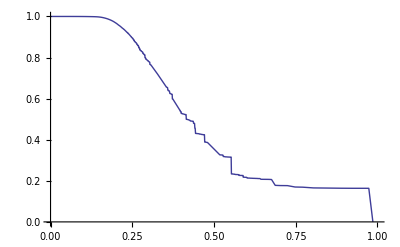

```mathematica
ParametricPlot[{vli[[1]][t],vli[[2]][t]},{t,0,1},PlotRange->{{0,1},{0,1}},AspectRatio->1/GoldenRatio]
```